```mathematica
Datos
```

```mathematica
Ni=50;
β=10^6;       
Ci=12.08;
Di=0.11;
ηLos=10^(1.6/10);
ηNLos=10^(23/10);
VC=3 10^8;
fc=2.5 10^9;
No=2.0019 10^-12;
Ki=1;
B=50 10^6;
Lxti=0;
Lxts=500;
Lyti=0;
Lyts=500;
Lzti=0;
Lzts=100;
Lxs={500,1000};
Lys={500,500};
Lxi={0,500};
Lyi={0,0};
Lzi={0,0};
Lzs={100,100};
μx=250;
μy=250;
μz=50;
σx=100;
σy=100;
σz=25;
α =2;
```

## Li and Joint

```mathematica
jointPDF3D[Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,x_,y_,z_,μx_,μy_,μz_,σx_,σy_,σz_]:=PDF[ProductDistribution[TruncatedDistribution[{Lxti,Lxts},NormalDistribution[μx,σx]],TruncatedDistribution[{Lyti,Lyts},NormalDistribution[μy,σy]],TruncatedDistribution[{Lzti,Lzts},NormalDistribution[μz,σz]]],{x,y,z}];
di[x_,xi_,y_,yi_,z_,hi_]:=Sqrt[(xi-x)^2+(yi-y)^2+(hi-z)^2];
βeta[x_,xi_,y_,yi_,z_,hi_]:=180/π ArcSin[(hi*Sqrt[(xi-x)^2+(yi-y)^2])/(di[x,xi,y,yi,z,hi] Sqrt[(xi-x)^2+(yi-y)^2+z^2])] ;
Plos[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_]:=1/(1+Ci ⅇ^(-Di ( βeta[x,xi,y,yi,z,hi]-Ci))) ;

Li1[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_,ηLos_,ηNLos_,fc_,VC_]:=Plos[x,xi,y,yi,hi,z,Ci,Di] *((4 Pi fc)/VC)^2 *di[x,xi,y,yi,z,hi]^α *ηLos +( ηNLos *(1- Plos[x,xi,y,yi,hi,z,Ci,Di])*di[x,xi,y,yi,z,hi]^α *((4 Pi fc)/VC)^2) ;

Mi[Ni_,Lxs_,Lys_,Lxi_,Lyi_,Lzs_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_, σy_,σz_ ]:= Ni* Abs[NIntegrate[jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,μx,μy,μz,σx,σy,σz],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}]];
```

## Función Objetivo

```mathematica
ptG3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,x_,y_,z_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=(2^((β Mi[Ni,Lxs,Lys,Lxi,Lyi,Lzs,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx, σy,σz])/B)-1)*No* Li1[x,xi,y,yi,z,hi,Ci,Di,ηLos,ηNLos,fc,VC]*jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,μx,μy,μz,σx,σy,σz];

ptGNint3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=NIntegrate[ptG3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B, Ni,x,y,z,xi,yi,hi,No,ηLos,ηNLos,fc,VC],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}];
ptTotalKiUAVs3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Sum[ptGNint3D[Ci,Di,Lxs[[i]],Lys[[i]],Lzs[[i]],Lxi[[i]],Lyi[[i]],Lzi[[i]],Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xi[[All,i]],yi[[All,i]],hi[[All,i]],No,ηLos,ηNLos,fc,VC],{i,1,Ki}];
```

## Llama la función

```mathematica
Objetivo1[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
xMod= ptTotalKiUAVs3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xi,yi,hi,No,ηLos,ηNLos,fc,VC];
Return[xMod];
]
```

## PSO-E-3D

```mathematica
PSOE3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,μx_,μy_,μz_,σx_,σy_,σz_,β_,B_,Ni_,No_,ηLos_,ηNLos_,fc_,VC_]:=Module[{},
iteration = 3;
popSize= 2000;
(*Parametrizaion of PSO*)
tao=1;
tao1=0.2;
inercia1=0.5;
memorial1=2;
cooperacion1=3;
perturbacion1=0.1;
(*Límites de las variables*)
Dmin={0,0,10};
Dmax={900,900,300};
(*Dmin=ConstantArray[0,3*Ki];
Dmax=ConstantArray[200,3*Ki];*)
(*Dmin= {0,0,0} ;
Dmax ={200,200,200} ;*)
D1=Length [Dmin];
xx=ConstantArray[0, {popSize,D1}];
v=ConstantArray[0, {popSize, D1}]; 
fitness=ConstantArray[0,popSize];
(*Posicion inicial de las particulas*)
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=(Dmax[[jj]]-Dmin[[jj]])RandomReal[{0,1}, popSize]+Dmin[[jj]]
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],xx[[All,(2*Ki)+1;;3*Ki]],No,ηLos,ηNLos,fc,VC];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=xx[[indgbest]];
fpbest=fitness;
xpbest=xx;
OF=ConstantArray[0, iteration];
For[count1=1, count1≤iteration, count1++,
OF[[count1]]=fgbest;
inercia = inercia1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
inercia=Clip[inercia,{0,1}];
memoria=memorial1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
memoria=Clip[memoria,{0,1}];
cooperacion=cooperacion1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
cooperacion=Clip[cooperacion,{0,1}];
xgbest=ConstantArray[xgbest,Length[xx]];
v=inercia*v+memoria*(xpbest-xx)+cooperacion*(xgbest-xx);
xx=xx+v;
xgbest=xgbest[[1]];
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y<Dmin[[jj]]]->Dmin[[jj]]];
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y>Dmax[[jj]]]->Dmax[[jj]]];
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],xx[[All,(2*Ki)+1;;3*Ki]],No,ηLos,ηNLos,fc,VC];
positions=Flatten[Position[Thread[fitness<fpbest],True]];
xpbest[[positions]]=xx[[positions]];
    fpbest[[positions]]=fitness[[positions]];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=Flatten[xx[[indgbest]]];
perturbacion=perturbacion1+tao1*Flatten[RandomReal[NormalDistribution[0,1],{1,Length[xgbest]}]];
perturbacion=Clip[perturbacion,{0,1}];
aux=xgbest+perturbacion;
aux={aux};
c1=Objetivo1[aux];
c2=c1[[1]];
If[fgbest>c2,
xgbest=aux;
xgbest=xgbest[[1]];
fgbest=Objetivo1[aux];
fgbest=fgbest[[1]];
];
];
Return[fgbest];
]
```

```mathematica
PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,σx,σy,σz,β,B,Ni,No,ηLos,ηNLos,fc,VC]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.0526058

```mathematica
AbsoluteTiming[Fig3D1=ParallelTable[{rho,PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,μx,μy,μz,1/rho,1/rho,σz,β,B,Ni,No,ηLos,ηNLos,fc,VC]},{rho,0.004,0.02,0.0004}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{16636.3,{{0.004,0.143117},{0.0044,0.138732},{0.0048,0.13413},{0.0052,0.129175},{0.0056,0.124075},{0.006,0.118773},{0.0064,0.113377},{0.0068,0.107896},{0.0072,0.102498},{0.0076,0.0971472},{0.008,0.0915117},{0.0084,0.0861892},{0.0088,0.0810152},{0.0092,0.0759689},{0.0096,0.0711401},{0.01,0.0665487},{0.0104,0.0621333},{0.0108,0.0579814},{0.0112,0.0540768},{0.0116,0.0504229},{0.012,0.0469906},{0.0124,0.043797},{0.0128,0.040833},{0.0132,0.0380875},{0.0136,0.0355484},{0.014,0.0332019},{0.0144,0.0311596},{0.0148,0.0290754},{0.0152,0.0271779},{0.0156,0.0254766},{0.016,0.0239224},{0.0164,0.0224572},{0.0168,0.0210888},{0.0172,0.0198497},{0.0176,0.0187043},{0.018,0.0176087},{0.0184,0.0166308},{0.0188,0.0157347},{0.0192,0.0148596},{0.0196,0.0140213},{0.02,0.0132783}}}

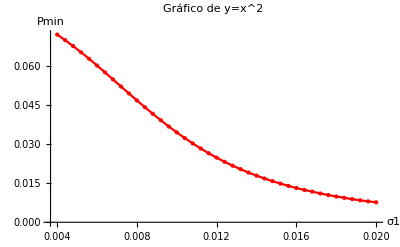

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

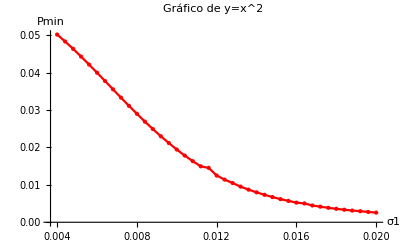

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\Urban-EPSO150F.mat",Fig3D1];
```

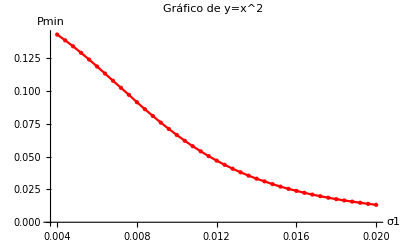

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\DenseUrbanEPSO-100.mat",Fig3D1];
```